## Creating a Collatz tree

### Introduction

This Mathematica notebook is licensed under a  . It provides a command showtree that constructs the function tree of the Collatz function generated by a set of integers. I hope anyone interested will feel free to improve this work and to use it in their own publications and coursework. 

This notebook is discussed in the post Generating a Collatz tree.

#### Define the function

```mathematica
cf[1]:=1;cf[n_Integer]:=If[ EvenQ[n],n/2,3n+1]
```

```mathematica
cf/@Range[1,10]
```

{1,1,10,2,16,3,22,4,28,5}

#### Find entries generated by an integer

```mathematica
fv[gl_List,n_Integer]:=(nn:=n;ggl:={nn};(Sow[1];While[!MemberQ[ggl,cf[nn]],(Sow[nn];Sow[cf[nn]]);nn=cf[nn]])//Reap)(*Sow[1] first to keep the output from being empty*)
```

```mathematica
findall[gl_List]:=((fv[gl,#][[2]][[1]]&/@gl)//Flatten//Union)
```

```mathematica
findall[{2,3,4}]
```

{1,2,3,4,5,8,10,16}

```mathematica
findall[{2,3}]
```

{1,2,3,4,5,8,10,16}

```mathematica
#->cf[#]&/@findall[{2,3,4}]
```

{1→1,2→1,3→10,4→2,5→16,8→4,10→5,16→8}

#### Construct the tree

```mathematica
showtree[gl_List]:=TreePlot[Drop[#->cf[#]&/@findall[gl],1],Bottom,1,VertexLabeling->True,ImageSize->Medium]
```

#### Examples

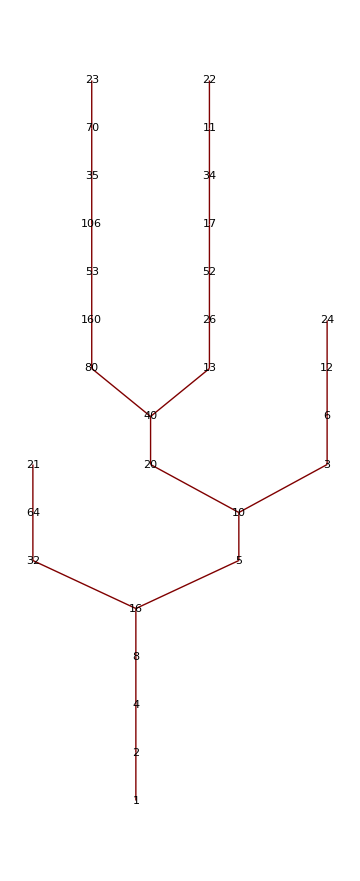

```mathematica
showtree[{2,3,17,21,23,22,24}]
```

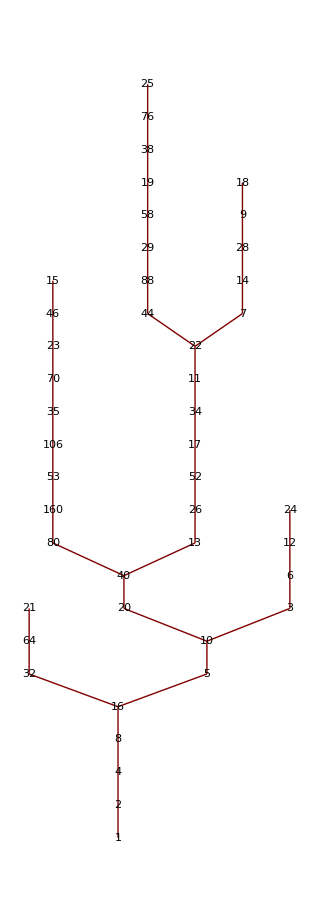

```mathematica
showtree[Range[2,26]]
```

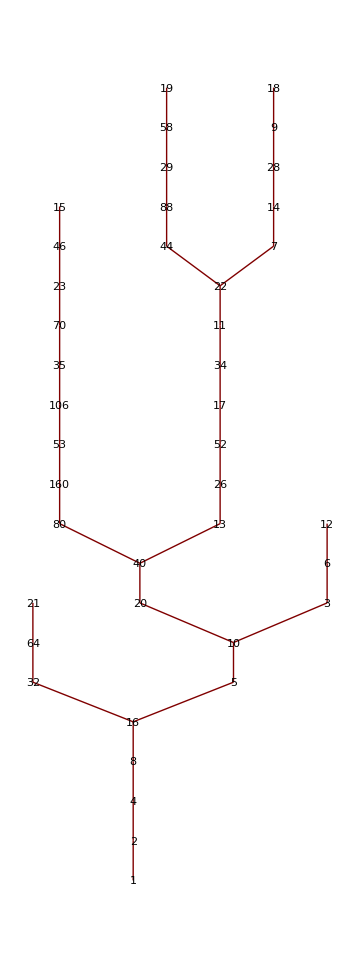

```mathematica
showtree[Range[2,21]]
```

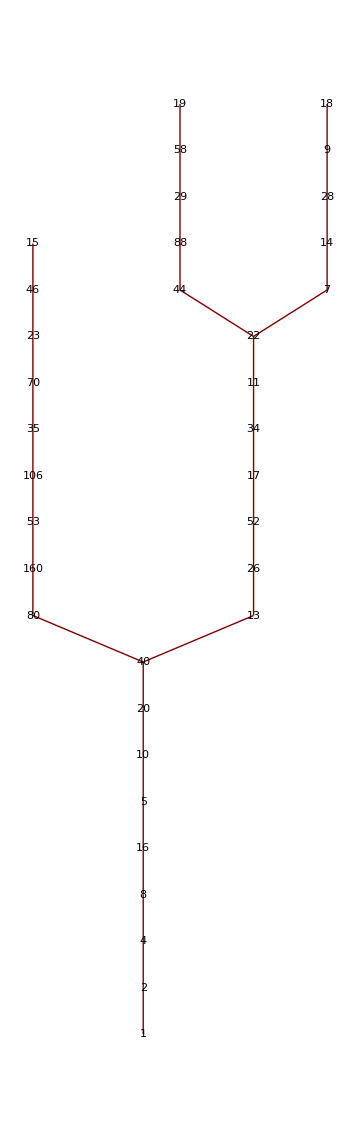

```mathematica
showtree[Range[15,19]]
```

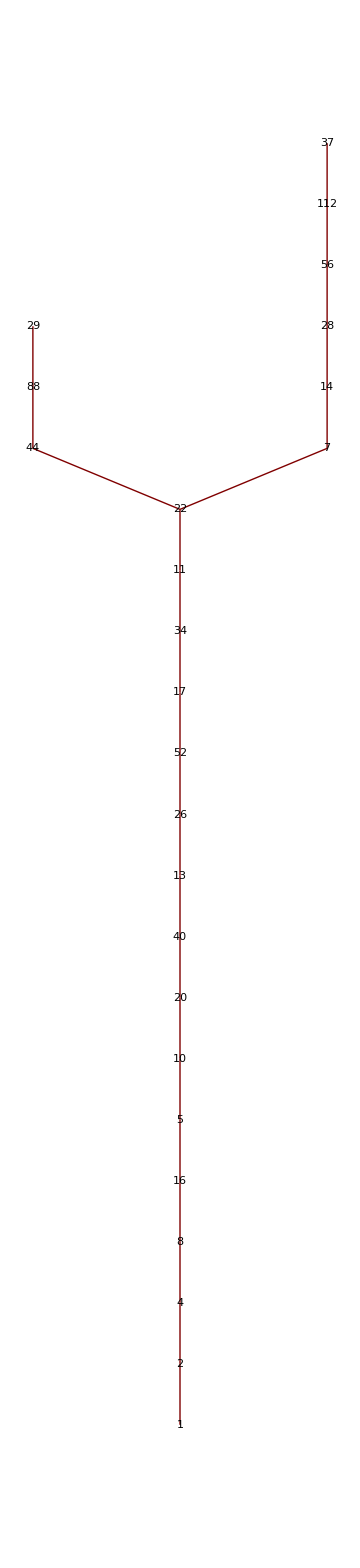

```mathematica
showtree[{29,37}]
```

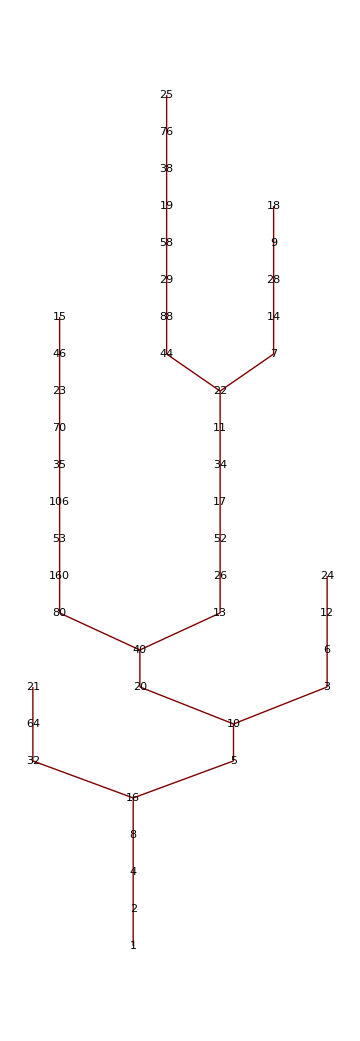

```mathematica
showtree[Select[Range[2,26],!PrimeQ[#]&]]
```

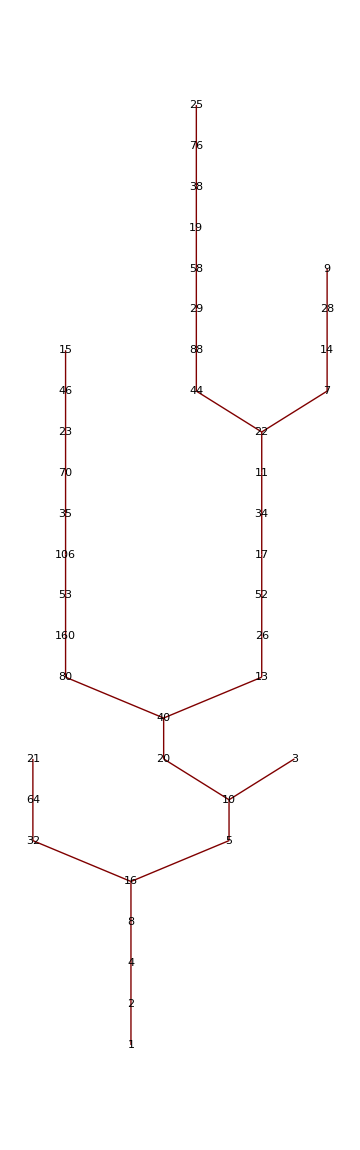

```mathematica
showtree[Select[Range[2,26],OddQ[#]&]]
```

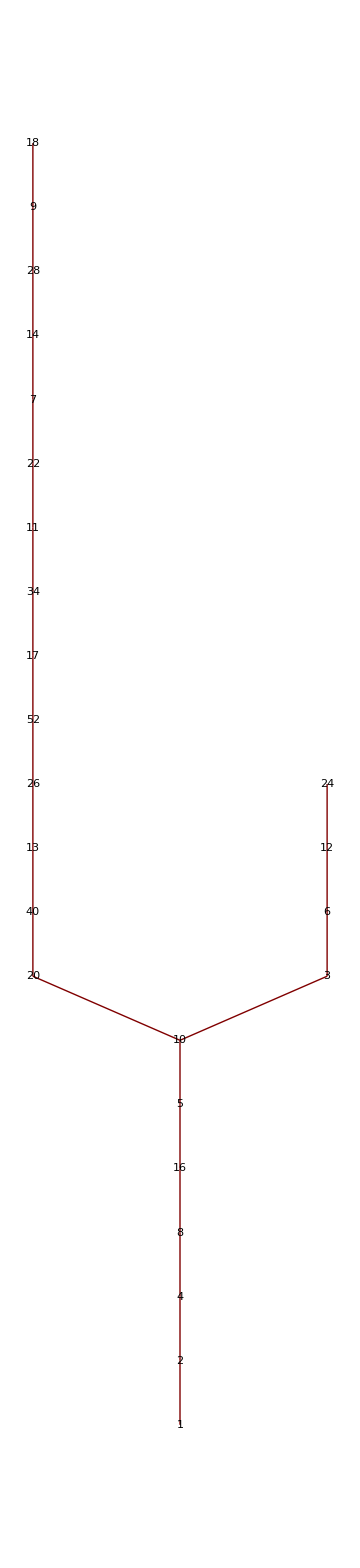

```mathematica
showtree[Select[Range[2,26],EvenQ[#]&]]
```

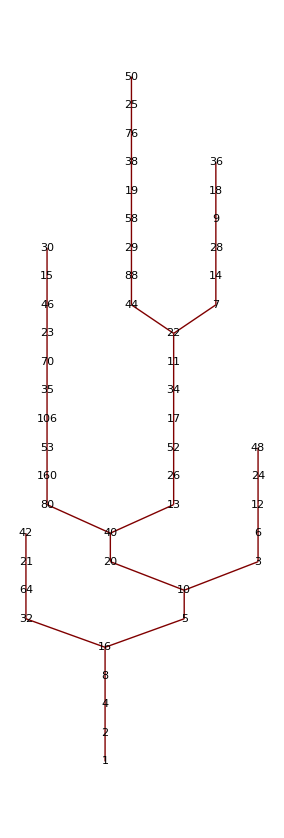

```mathematica
showtree[Select[Range[2,50],EvenQ[#]&]]
```